```mathematica
Quit[]
```

## Electoral votes

Electoral votes, according to https://en.wikipedia.org/wiki/United_States_Electoral_College#Current_electoral_vote_distribution .

```mathematica
ev=<|
"California"->55,
"Texas"->38,
"Florida"->29,"New York"->29,
"Illinois"->20,"Pennsylvania"->20,
"Ohio"->18,
"Georgia"->16,"Michigan"->16,
"North Carolina"->15,
"New Jersey"->14,
"Virginia"->13,
"Washington"->12,
"Arizona"->11,"Indiana"->11,"Massachusetts"->11,"Tennessee"->11,
"Maryland"->10,"Minnesota"->10,"Missouri"->10, "Wisconsin"->10,
"Alabama"->9,"Colorado"->9, "South Carolina"->9,
"Kentucky"->8, "Louisiana"->8,
"Connecticut"->7, "Oklahoma"->7, "Oregon"->7,
"Arkansas"-> 6,"Iowa"->6,"Kansas"->6, "Mississippi"->6, "Nevada"->6,"Utah"->6,
"Nebraska"->5, "New Mexico"->5, "West Virginia"-> 5,
"Hawaii"->4,"Idaho"->4,"Maine"->4,"New Hampshire"->4,"Rhode Island"->4,
"Alaska"->3,"Delaware"->3,"District of Columbia"->3,"Montana"->3,"North Dakota"->3,"South Dakota"->3,"Vermont"->3,"Wyoming"->3
|>;
```

```mathematica
ev//Values//Total
```

538

```mathematica
ev//Length
```

51

```mathematica
splitVotes={"Nebraska", "Maine"};
```

## Summarizing state arrival deadlines

Allowed delays between postmarking / mailing and arrival, by days after election day votes will still count.  According to https://www.ncsl.org/research/elections-and-campaigns/vopp-table-11-receipt-and-postmark-deadlines-for-absentee-ballots.aspx and https://www.vote.org/absentee-ballot-deadlines/ .

```mathematica
delays=<|
"Alaska"->10,
"California"->17,(* updated 3 to 17 *)
"District of Columbia"->7, (* updated 7 to 10 *)
"Florida"->0 (* MAYBE *),
"Illinois"->14,
"Iowa"->6 (* Monday following the Tuesday election *),
"Kansas"->3,
"Maryland"->10 (* MAYBE *),
"Mississippi" -> 5, (* updated from 0 to 5 *)
"New Jersey"->7, (* updated from 2 to 7 *)
"New York"->7,
"North Carolina"->9, (* updated from 3 to 9 *)
"North Dakota"->0 (* before the canvass *),
"Ohio"->10,
"Texas"->1,
"Pennsylvania"->3,(* updated from 0 to 3, litigation pending? *)
"Utah"->14 (* 7 to 14, before county canvass *),
"Virginia"->3,
"Washington"->5,
"West Virginia" ->6 (* updated from 5 to 6 *)
|>;
```

```mathematica
delays // Length
```

20

```mathematica
Union[Keys[delays],Keys[ev]]//Length
```

51

```mathematica
horizon=18 (* days *);
```

```mathematica
(* symplify notation *)
electionDay=DateObject["2020-11-03"];
deadline[n_]:=electionDay+Quantity[n,"Days"]

(* deadline of every state by date *)
deadlines=Keys[ev]//AssociationMap[deadline[Lookup[delays,#,0 (* default *)]]&];

(* date -> states *)
deadlinesByDay=Association@Table[
deadline[x]->Keys@Select[
deadlines,
deadline[x-1]<#≤deadline[x]&
],
{x,-1,horizon}
];
```

```mathematica
deadlinesByDay//Normal//TableForm
```

Day: Mon 2 Nov 2020→{}
Day: Tue 3 Nov 2020→{Florida,Georgia,Michigan,Arizona,Indiana,Massachusetts,Tennessee,Minnesota,Missouri,Wisconsin,Alabama,Colorado,South Carolina,Kentucky,Louisiana,Connecticut,Oklahoma,Oregon,Arkansas,Nevada,Nebraska,New Mexico,Hawaii,Idaho,Maine,New Hampshire,Rhode Island,Delaware,Montana,North Dakota,South Dakota,Vermont,Wyoming}
Day: Wed 4 Nov 2020→{Texas}
Day: Thu 5 Nov 2020→{}
Day: Fri 6 Nov 2020→{Pennsylvania,Virginia,Kansas}
Day: Sat 7 Nov 2020→{}
Day: Sun 8 Nov 2020→{Washington,Mississippi}
Day: Mon 9 Nov 2020→{Iowa,West Virginia}
Day: Tue 10 Nov 2020→{New York,New Jersey,District of Columbia}
Day: Wed 11 Nov 2020→{}
Day: Thu 12 Nov 2020→{North Carolina}
Day: Fri 13 Nov 2020→{Ohio,Maryland,Alaska}
Day: Sat 14 Nov 2020→{}
Day: Sun 15 Nov 2020→{}
Day: Mon 16 Nov 2020→{}
Day: Tue 17 Nov 2020→{Illinois,Utah}
Day: Wed 18 Nov 2020→{}
Day: Thu 19 Nov 2020→{}
Day: Fri 20 Nov 2020→{California}
Day: Sat 21 Nov 2020→{}

```mathematica
votesByDayLabeled=deadlinesByDay//Map[Function[{states},
Labeled[
Total@Map[Lookup[ev,#]&,states],
ToString@states,
Right
]
]];
```

```mathematica
votesByDayLabeled//Values//Map[First]//Total
```

538

```mathematica
votesByDayLabeled//Select[First[#]>0&]//Normal//TableForm
```

Day: Tue 3 Nov 2020→259{Florida, Georgia, Michigan, Arizona, Indiana, Massachusetts, Tennessee, Minnesota, Missouri, Wisconsin, Alabama, Colorado, South Carolina, Kentucky, Louisiana, Connecticut, Oklahoma, Oregon, Arkansas, Nevada, Nebraska, New Mexico, Hawaii, Idaho, Maine, New Hampshire, Rhode Island, Delaware, Montana, North Dakota, South Dakota, Vermont, Wyoming}
Day: Wed 4 Nov 2020→38{Texas}
Day: Fri 6 Nov 2020→39{Pennsylvania, Virginia, Kansas}
Day: Sun 8 Nov 2020→18{Washington, Mississippi}
Day: Mon 9 Nov 2020→11{Iowa, West Virginia}
Day: Tue 10 Nov 2020→46{New York, New Jersey, District of Columbia}
Day: Thu 12 Nov 2020→15{North Carolina}
Day: Fri 13 Nov 2020→31{Ohio, Maryland, Alaska}
Day: Tue 17 Nov 2020→26{Illinois, Utah}
Day: Fri 20 Nov 2020→55{California}

## Graph: Electoral votes countable per day

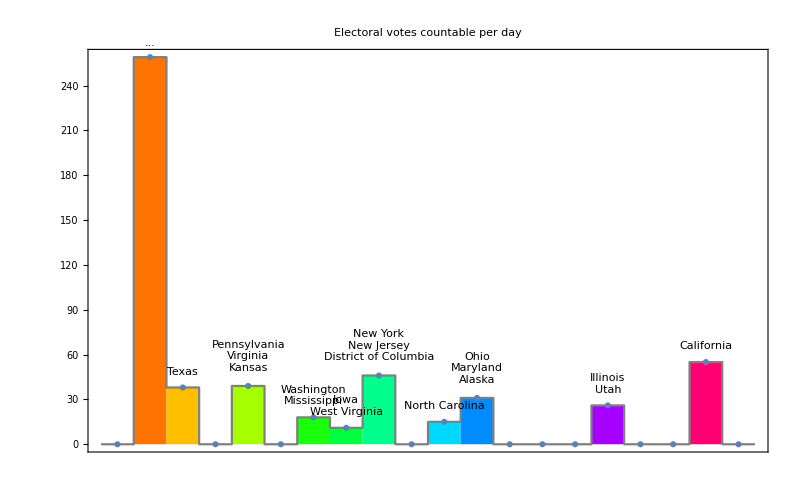

```mathematica
votesByDay=deadlinesByDay//Map[Function[{states},
states//Map[Lookup[ev,#]&]//Total
]];

stateList=Function[
{point, position},
Module[
{day, label},
day=DayRound@DateObject@First[point];
label=Lookup[deadlinesByDay,day, FIXME];

If[
MatchQ[label,{}],
label = ""
];

If[
Length[label]>20,
label="..."
];

Placed[
TableForm@label,
(* position of label *)
Top
]
]];

DateListStepPlot[
votesByDay,
Center,
PlotLabel -> "Electoral votes countable per day",
LabelingFunction->(stateList),
PlotMarkers->Automatic,
PlotRange->All,
GridLines->Automatic,
ColorFunction->Function[{x,y},Hue[x]],
Filling->Axis
]
```

## Graph: Cumulative electoral votes countable by day

```mathematica
cumulativeDeadlinesByDay=Association@Table[
deadline[x]->Keys@Select[
deadlines,
#≤deadline[x]&
],
{x,-1,horizon}
];
```

```mathematica
cumulativeVotesByDay=cumulativeDeadlinesByDay//Map[Function[{states},
states//Map[Lookup[ev,#]&]//Total
]]
```

<|Day: Mon 2 Nov 2020→0,Day: Tue 3 Nov 2020→259,Day: Wed 4 Nov 2020→297,Day: Thu 5 Nov 2020→297,Day: Fri 6 Nov 2020→336,Day: Sat 7 Nov 2020→336,Day: Sun 8 Nov 2020→354,Day: Mon 9 Nov 2020→365,Day: Tue 10 Nov 2020→411,Day: Wed 11 Nov 2020→411,Day: Thu 12 Nov 2020→426,Day: Fri 13 Nov 2020→457,Day: Sat 14 Nov 2020→457,Day: Sun 15 Nov 2020→457,Day: Mon 16 Nov 2020→457,Day: Tue 17 Nov 2020→483,Day: Wed 18 Nov 2020→483,Day: Thu 19 Nov 2020→483,Day: Fri 20 Nov 2020→538,Day: Sat 21 Nov 2020→538|>

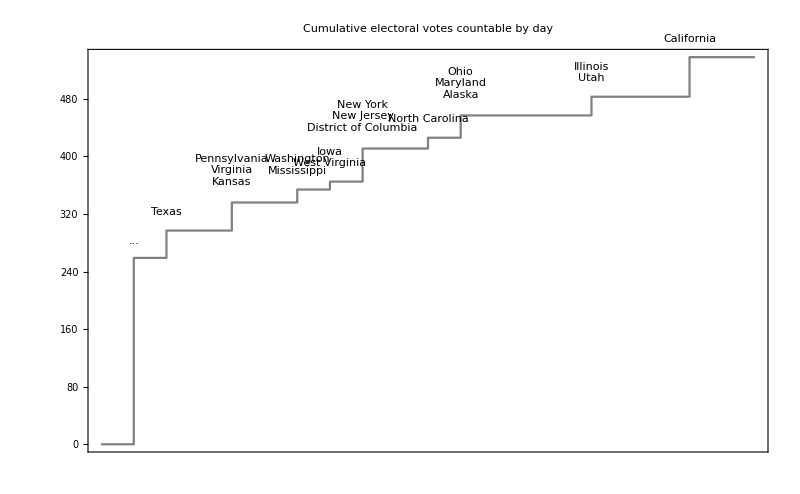

```mathematica
stateList2=Function[
{point, position},
Module[
{day, label},
day=DayRound@DateObject@First[point];
label=Lookup[deadlinesByDay,day, FIXME];

If[
MatchQ[label,{}],
label = ""
];

If[
Length[label]>20,
label="..."
];

Placed[
TableForm@label,
(* position of label *)
Top
]
]];

DateListStepPlot[
cumulativeVotesByDay,
Right,
PlotLabel -> "Cumulative electoral votes countable by day",
LabelingFunction->(stateList2),
PlotRange->All,
GridLines->Automatic,
ColorFunction->Function[{x,y},Hue[x]]
]
```